```mathematica
Plot3D[Sin[x^2 + y^2], {x, -10, 10}, {y, -10, 10}]
Plot3D[Sin[x^2 + y^2], {x, 8, 10}, {y, -1, 1}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[Plot3D[Sin[x^2 + y^2], {x, -10, 10}, {y, -10, 10}],ViewPoint->{0,0,∞}]
```

-Graphics3D-

```mathematica
ContourPlot[Sin[x^2 + y^2], {x, -10, 10}, {y, -10, 10}]
```

-Graphics-

```mathematica
PlotFn[lo_, hi_] :=Plot[{Mod[x^2, 255], Mod[(x - 255)^2, 255]}, {x, lo , hi}, GridLines-> {Table[{i, Dashed}, {i, lo, hi}] , {}}]
```

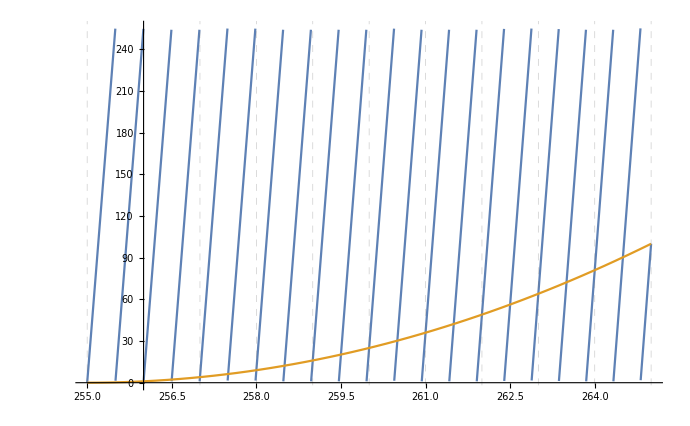

```mathematica
PlotFn[255, 265] (* plot from 255 .. 265. Note that the quadratic follows it exactly. Note that we have two lines for each pixel. *)
```

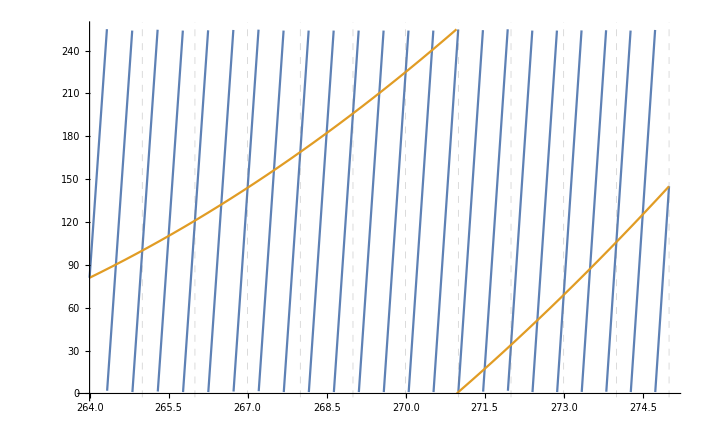

```mathematica
PlotFn[264,275] (* plot for the next ten pixels. Note that we continue to intersect on the quadratic even with the modulo*)
```

```mathematica
PlotFnHalf[lo_, hi_] :=Plot[{Mod[x^2, 255], Mod[(x - 255/2)^2 + 64, 255]}, {x, lo , hi}, GridLines-> {Table[{i, Dashed}, {i, lo, hi}] , {}}]
(* generate a plot at the M = 1/2 band *)
```

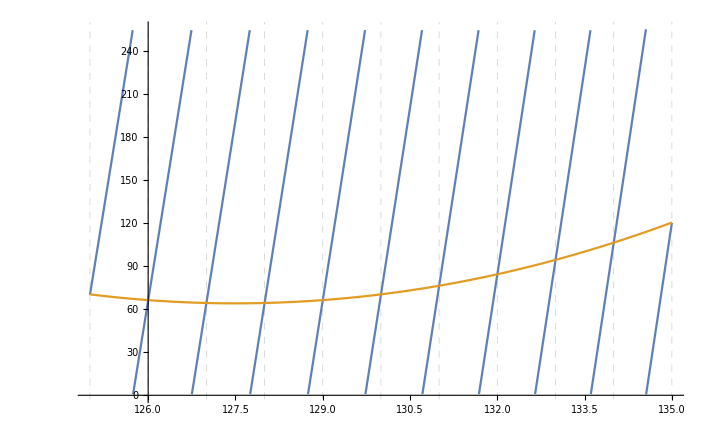

```mathematica
PlotFnHalf[125, 135]
```

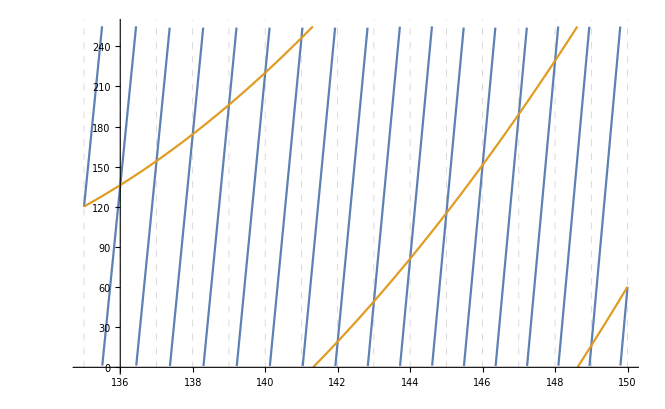

```mathematica
PlotFnHalf[135, 150]
```

```mathematica
PlotFn[lo_, hi_, alpha_] :=Show[
ListLinePlot[Table[{k, Mod[alpha k^2, 255]}, {k, lo, hi}], MaxPlotPoints-> (hi - lo), PlotStyle->Orange],
Plot[{Mod[alpha x^2, 255]}, {x, lo , hi}, GridLines-> {Table[{i, Dashed}, {i, lo, hi}] , {}}] , PlotRange -> All

]

(* add in alpha *)
```

```mathematica
Manipulate[PlotFn[260, 270, a], {a, 1 - 10/255, 1 - 11/255}]
```

```mathematica
Mod[1.0005 255^2, 255]
```

32.5125

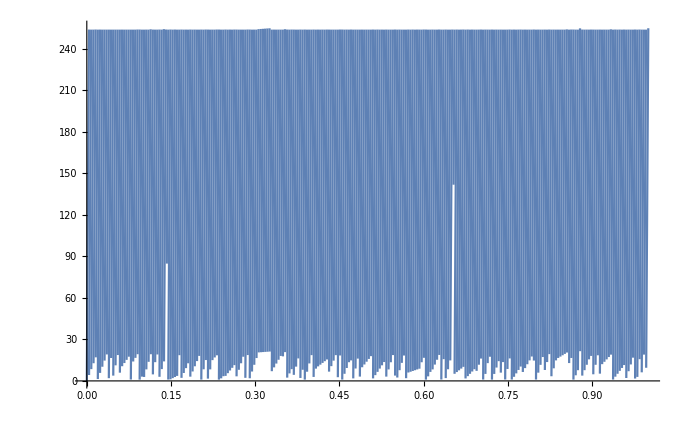

```mathematica
Plot[Mod[x 255^2, 255], {x, 0, 1}]
```

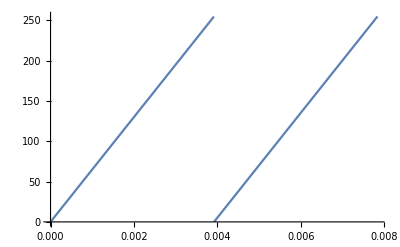

```mathematica
Plot[Mod[x 255^2,255],{x,0,1/255 + 1/255}]
```

```mathematica
Mod[alpha 255^2, 255]
```

Mod[65025 alpha,255]

```mathematica
(* We notice that given alpha, there is a minimum in the parabola at x = 255 - (alpha - 1) 255, when 2 > alpha ≥ 1 *)
(* We also notice that there's a minimum 0 for alpha = k/255+1 when 0 ≤ k < 255 at x = 255 + k (or (alpha - 1)255) *)
(* This means if we increase alpha by 1/255 over 1 second we will have a smooth transition to the next wave in 1 second *)
```

```mathematica
N[1 - 2/255]
```

0.992157